## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="G6PDH2r";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp3.csv";

mainFolder = "fit_G6PDH2r_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiologicall,Q10];
```

(g6p^c+nadp^c⇌(6pgl)^c+nadph^c)^G6PDH2r

random sequential (nad); ordered sequential (nadp); [nad||g6p,g6p||nad,6pgl,nadh],[nadp,g6p,6pgl,nadph]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadp | Null
g6p | Null | 12.9 | 12.255
13.545 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p | 0.000145 | 0.00013775
0.00015225 | nadp | 0.00018 | M | 8 | 25 | trishcl | 0.1 | mg2 | 0.01
cl | 0.02
1 | nadp | 0.000015 | 0.00001425
0.00001575 | g6p | 0.001 | M | 8 | 25 | trishcl | 0.1 | mg2 | 0.01
cl | 0.02
1 | nad | 0.00167 | 0.0015865
0.0017535 | g6p | 0.001 | M | 8 | 25 | trishcl | 0.1 | mg2 | 0.01
cl | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,0};
s05Priorities = Null;
kcatPriorities = Null;
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g6p^c+nadp^c⇌(6pgl)^c+nadph^c)^G6PDH2r

random sequential (nad); ordered sequential (nadp); [nad||g6p,g6p||nad,6pgl,nadh],[nadp,g6p,6pgl,nadph]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadp | Null
g6p | Null | 12.9 | 12.255
13.545 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p | 0.000145 | 0.00013775
0.00015225 | nadp | 0.00018 | M | 8 | 25 | trishcl | 0.1 | mg2 | 0.01
cl | 0.02
1 | nadp | 0.000015 | 0.00001425
0.00001575 | g6p | 0.001 | M | 8 | 25 | trishcl | 0.1 | mg2 | 0.01
cl | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_G6PDH2r[c] + nadp[c] <=> E_G6PDH2r[c]&nadp",
				"E_G6PDH2r[c]&nadp + g6p[c] <=> E_G6PDH2r[c]&nadp&g6p",
				"E_G6PDH2r[c]&nadp&g6p <=> E_G6PDH2r[c]&6pgl&nadph",
				"E_G6PDH2r[c]&6pgl&nadph <=> E_G6PDH2r[c]&6pgl + nadph[c]",
				"E_G6PDH2r[c]&6pgl <=> E_G6PDH2r[c] + 6pgl[c]"};



enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((G6PDH2r^c)_^+nadp^c⇌(G6PDH2r^c&nadp^c)_^)^G6PDH2r1,((G6PDH2r^c&(6pgl)^c)_^⇌(G6PDH2r^c)_^+(6pgl)^c)^G6PDH2r2,((G6PDH2r^c&nadp^c)_^+g6p^c⇌(G6PDH2r^c&nadp^c&g6p^c)_^)^G6PDH2r3,((G6PDH2r^c&(6pgl)^c&nadph^c)_^⇌(G6PDH2r^c&(6pgl)^c)_^+nadph^c)^G6PDH2r4,((G6PDH2r^c&nadp^c&g6p^c)_^⇌(G6PDH2r^c&(6pgl)^c&nadph^c)_^)^G6PDH2r5}

```mathematica
Print[enzymeModel]
```

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((G6PDH2r^c)_^+nadp^c⇌(G6PDH2r^c&nadp^c)_^)^G6PDH2r1,Overscript[(G6PDH2r^c&(6pgl)^c)_^⇌(G6PDH2r^c)_^+(6pgl)^c, G6PDH2r2],((G6PDH2r^c&nadp^c)_^+g6p^c⇌(G6PDH2r^c&nadp^c&g6p^c)_^)^G6PDH2r3,Overscript[(G6PDH2r^c&(6pgl)^c&nadph^c)_^⇌(G6PDH2r^c&(6pgl)^c)_^+nadph^c, G6PDH2r4],((G6PDH2r^c&nadp^c&g6p^c)_^⇌(G6PDH2r^c&(6pgl)^c&nadph^c)_^)^G6PDH2r5};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((G6PDH2r^c&nadp^c&g6p^c)_^-((G6PDH2r^c&(6pgl)^c&nadph^c)_^)/K_G6PDH2r5) Volume_c k_G6PDH2r5^⟶}

Volume_c (-(G6PDH2r^c&(6pgl)^c&nadph^c)_^ k_G6PDH2r5^⟵+(G6PDH2r^c&nadp^c&g6p^c)_^ k_G6PDH2r5^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
Print[enzymeModel]
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

```mathematica
Print[enzymeModel]
```

```mathematica
FilePrint@dataPathList
```

Priority	6pgl[c]	g6p[c]	nadp[c]	nadph[c]	param_G6PDH2r_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt"	12.9
1	0	0.000014499999999999983	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.09090909090909083
1	0	0.000022980951290686127	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.13680688860320991
1	0	0.0000364223532568889	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.20076000891310172
1	0	0.00005772553973025699	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.284747248950801
1	0	0.00009148881494962787	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.3868631798468566
1	0	0.00014499999999999984	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.4999999999999997
1	0	0.00022980951290686128	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.6131368201531429
1	0	0.000364223532568889	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.7152527510491985
1	0	0.0005772553973025704	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.7992399910868981
1	0	0.0009148881494962787	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.8631931113967897
1	0	0.0014499999999999984	0.00018	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt"	0.909090909090909
1	0	0.001	1.5000000000000005e-6	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.09090909090909093
1	0	0.001	2.377339788691672e-6	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.13680688860321008
1	0	0.001	3.767829647264374e-6	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.20076000891310192
1	0	0.001	5.971607558302455e-6	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.2847472489508013
1	0	0.001	9.464360167202897e-6	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.3868631798468569
1	0	0.001	0.000015000000000000004	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.5
1	0	0.001	0.000023773397886916717	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.6131368201531432
1	0	0.001	0.000037678296472643745	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.7152527510491988
1	0	0.001	0.000059716075583024555	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.799239991086898
1	0	0.001	0.00009464360167202897	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.86319311139679
1	0	0.001	0.00015000000000000004	0	1	8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt"	0.909090909090909

### Simulate data with uncertainty

```mathematica
nSamples=100;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

Simulating Keq data...

Simulating Km data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	100
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateRev_6pgl.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateRev_nadph.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateRev_6pgl.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateRev_nadph.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.05753119769
best_fit: 0.391861435323
best_fit: 0.72329540897
best_fit: 0.593219961835
best_fit: 0.52668169021
best_fit: 0.820127557228
best_fit: 0.465613830093
best_fit: 0.962515700054
best_fit: 0.418136755387
best_fit: 0.380548052195
best_fit: 0.134178260327
best_fit: 1.02194883303
best_fit: 0.655320402956
best_fit: 0.949369453267
best_fit: 0.7070977123
best_fit: 0.942374325549
best_fit: 0.573584112939
best_fit: 0.954893469596
best_fit: 0.922438232549
best_fit: 0.982823493534
best_fit: 0.473237638533
best_fit: 0.182236233565
best_fit: 0.332346070668
best_fit: 0.252187472049
best_fit: 0.854846202089
best_fit: 1.01484202486
best_fit: 0.252112998102
best_fit: 1.08303580346
best_fit: 0.733244050323
best_fit: 0.16594118799
best_fit: 1.04489046981
best_fit: 1.0145636262
best_fit: 0.239927439362
best_fit: 0.979166646448
best_fit: 1.06459497291
best_fit: 0.306831079474
best_fit: 0.613571022493
best_fit: 0.613674455599
best_fit: 0.867518894939
best_fit: 0.53990015057
best_fit: 0.790212142657
best_fit: 1.01635980537
best_fit: 0.980238373738
best_fit: 0.359782276792
best_fit: 0.442474723498
best_fit: 0.759096298245
best_fit: 0.835297826177
best_fit: 1.0096070468
best_fit: 1.01917536907
best_fit: 1.04127177143
best_fit: 0.336593023573
best_fit: 0.110378739843
best_fit: 1.06721032588
best_fit: 0.275497513427
best_fit: 1.08688974455
best_fit: 0.447506580608
best_fit: 0.811773469425
best_fit: 0.678442147241
best_fit: 0.962800037234
best_fit: 0.603492526094
best_fit: 1.09389708895
best_fit: 0.732074166217
best_fit: 0.677737399641
best_fit: 1.03326939557
best_fit: 0.9437941574
best_fit: 1.07608213329
best_fit: 0.365600603066
best_fit: 0.152945330665
best_fit: 0.852053922705
best_fit: 0.139151547506
best_fit: 0.391414677822
best_fit: 0.628972416129
best_fit: 0.386397433769
best_fit: 0.771844292071
best_fit: 0.910401661569
best_fit: 0.405403682255
best_fit: 0.631611789018
best_fit: 0.585035073334
best_fit: 0.142033574844
best_fit: 0.529627161165
best_fit: 0.656807666431
best_fit: 0.522490573203
best_fit: 1.03404468434
best_fit: 0.88777467714
best_fit: 0.783367014021
best_fit: 0.272547653629
best_fit: 1.03598764011
best_fit: 1.05876999575
best_fit: 0.933403705978
best_fit: 0.565574232196
best_fit: 0.674686487103
best_fit: 0.609693899333
best_fit: 0.97591449303
best_fit: 0.972245407408
best_fit: 0.121761948777
best_fit: 0.921212475104
best_fit: 1.08930603417
best_fit: 0.555162706095
best_fit: 1.05688150143
best_fit: 1.08333400916

```mathematica
Print[paramFitSub]
```

paramFitSub

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 4.25752×10^-10 | 1.81264×10^-19 | 1.26463×10^-8 | 9.8033×10^-8 | 12.9 | 12.9
1 | haldaneRatio_1 | 4.25752×10^-10 | 1.81264×10^-19 | 1.26463×10^-8 | 9.8033×10^-8 | 12.9 | 12.9
1 | haldaneRatio_1 | 4.25752×10^-10 | 1.81264×10^-19 | 1.26463×10^-8 | 9.8033×10^-8 | 12.9 | 12.9
1 | haldaneRatio_1 | 4.25752×10^-10 | 1.81264×10^-19 | 1.26463×10^-8 | 9.8033×10^-8 | 12.9 | 12.9
1 | haldaneRatio_1 | 4.25752×10^-10 | 1.81264×10^-19 | 1.26463×10^-8 | 9.8033×10^-8 | 12.9 | 12.9
1 | haldaneRatio_1 | 4.25752×10^-10 | 1.81264×10^-19 | 1.26463×10^-8 | 9.8033×10^-8 | 12.9 | 12.9
1 | haldaneRatio_1 | 4.25752×10^-10 | 1.81264×10^-19 | 1.26463×10^-8 | 9.8033×10^-8 | 12.9 | 12.9
1 | haldaneRatio_1 | 4.25752×10^-10 | 1.81264×10^-19 | 1.26463×10^-8 | 9.8033×10^-8 | 12.9 | 12.9
1 | haldaneRatio_1 | 4.25752×10^-10 | 1.81264×10^-19 | 1.26463×10^-8 | 9.8033×10^-8 | 12.9 | 12.9
1 | haldaneRatio_1 | 4.25752×10^-10 | 1.81264×10^-19 | 1.26463×10^-8 | 9.8033×10^-8 | 12.9 | 12.9
1 | haldaneRatio_1 | 4.25752×10^-10 | 1.81264×10^-19 | 1.26463×10^-8 | 9.8033×10^-8 | 12.9 | 12.9
1 | relRateFor_g6p | 0.0000233846 | 5.46841×10^-10 | 4.89488×10^-6 | 0.00538436 | 0.0909091 | 0.0909042
1 | relRateFor_g6p | 0.0000190246 | 3.61936×10^-10 | 5.9928×10^-6 | 0.00438048 | 0.136807 | 0.136801
1 | relRateFor_g6p | 0.0000129494 | 1.67686×10^-10 | 5.98597×10^-6 | 0.00298165 | 0.20076 | 0.200754
1 | relRateFor_g6p | 4.97083×10^-6 | 2.47091×10^-11 | 3.25913×10^-6 | 0.00114457 | 0.284747 | 0.284744
1 | relRateFor_g6p | 4.73007×10^-6 | 2.23736×10^-11 | 4.2135×10^-6 | 0.00108914 | 0.386863 | 0.386867
1 | relRateFor_g6p | 0.0000154782 | 2.39574×10^-10 | 0.0000178202 | 0.00356405 | 0.5 | 0.500018
1 | relRateFor_g6p | 0.0000262266 | 6.87833×10^-10 | 0.0000370278 | 0.00603907 | 0.613137 | 0.613174
1 | relRateFor_g6p | 0.0000359282 | 1.29083×10^-9 | 0.0000591736 | 0.00827311 | 0.715253 | 0.715312
1 | relRateFor_g6p | 0.0000439076 | 1.92788×10^-9 | 0.000080808 | 0.0101106 | 0.79924 | 0.799321
1 | relRateFor_g6p | 0.0000499837 | 2.49837×10^-9 | 0.0000993521 | 0.0115098 | 0.863193 | 0.863292
1 | relRateFor_g6p | 0.0000543445 | 2.95332×10^-9 | 0.000113764 | 0.0125141 | 0.909091 | 0.909205
1 | relRateFor_nadp | 2.42015×10^-6 | 5.85711×10^-12 | 5.06598×10^-7 | 0.000557258 | 0.0909091 | 0.0909086
1 | relRateFor_nadp | 1.96906×10^-6 | 3.87721×10^-12 | 6.20272×10^-7 | 0.000453392 | 0.136807 | 0.136806
1 | relRateFor_nadp | 1.34053×10^-6 | 1.79702×10^-12 | 6.19681×10^-7 | 0.000308667 | 0.20076 | 0.200759
1 | relRateFor_nadp | 5.15096×10^-7 | 2.65324×10^-13 | 3.37725×10^-7 | 0.000118605 | 0.284747 | 0.284747
1 | relRateFor_nadp | 4.88508×10^-7 | 2.3864×10^-13 | 4.35156×10^-7 | 0.000112483 | 0.386863 | 0.386864
1 | relRateFor_nadp | 1.60043×10^-6 | 2.56137×10^-12 | 1.84256×10^-6 | 0.000368513 | 0.5 | 0.500002
1 | relRateFor_nadp | 2.71235×10^-6 | 7.35685×10^-12 | 3.82931×10^-6 | 0.000624544 | 0.613137 | 0.613141
1 | relRateFor_nadp | 3.71596×10^-6 | 1.38084×10^-11 | 6.11996×10^-6 | 0.000855636 | 0.715253 | 0.715259
1 | relRateFor_nadp | 4.5414×10^-6 | 2.06244×10^-11 | 8.35767×10^-6 | 0.0010457 | 0.79924 | 0.799248
1 | relRateFor_nadp | 5.16995×10^-6 | 2.67284×10^-11 | 0.0000102757 | 0.00119043 | 0.863193 | 0.863203
1 | relRateFor_nadp | 5.62104×10^-6 | 3.15961×10^-11 | 0.0000117664 | 0.0012943 | 0.909091 | 0.909103

### Simulated Data and Best Fit Data Plot

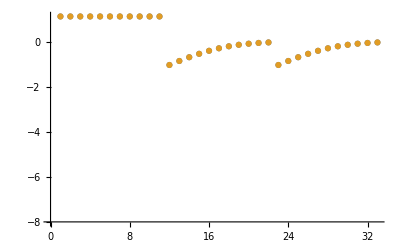

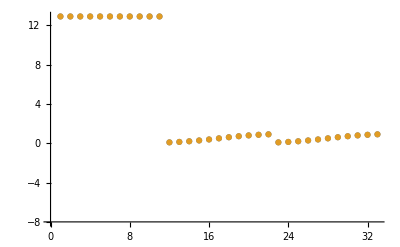

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

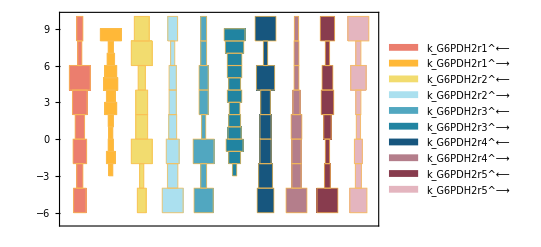

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

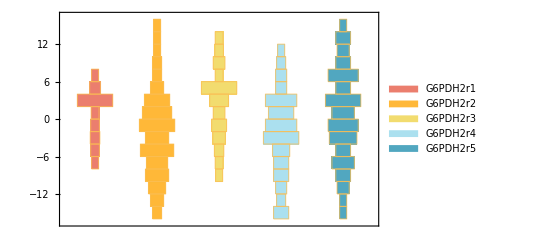

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

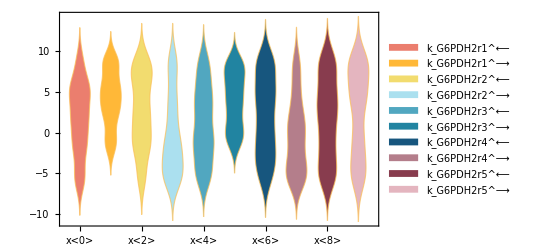

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

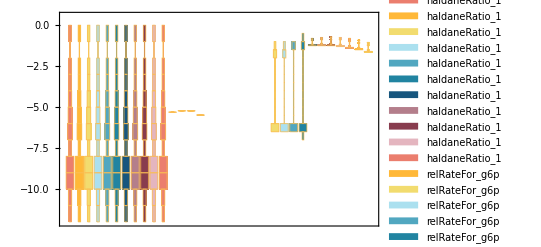

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.000145 | 0.00014499 | 0.00712681
0.000015 | 0.0000149999 | 0.000737012

```mathematica
Print[relativeRateForward]
```

{(g6p^c (k_G6PDH2r2^⟶ k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r1^⟵ k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶)+nadp^c k_G6PDH2r1^⟶ (k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r3^⟶ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵+k_G6PDH2r5^⟶)))))/(g6p^c k_G6PDH2r2^⟶ k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r1^⟵ k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶)+nadp^c k_G6PDH2r1^⟶ (g6p^c k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+g6p^c k_G6PDH2r3^⟶ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵+k_G6PDH2r5^⟶)))),(nadp^c (g6p^c k_G6PDH2r1^⟶ k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+g6p^c k_G6PDH2r2^⟶ k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r1^⟵ k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶)+k_G6PDH2r1^⟶ k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+g6p^c k_G6PDH2r3^⟶ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵+k_G6PDH2r5^⟶))))/(g6p^c k_G6PDH2r2^⟶ k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r1^⟵ k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶)+nadp^c k_G6PDH2r1^⟶ (g6p^c k_G6PDH2r3^⟶ k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+k_G6PDH2r2^⟶ (k_G6PDH2r3^⟵ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵)+k_G6PDH2r4^⟶ k_G6PDH2r5^⟶+g6p^c k_G6PDH2r3^⟶ (k_G6PDH2r4^⟶+k_G6PDH2r5^⟵+k_G6PDH2r5^⟶))))}

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
12.9 | 12.9 | 9.8033×10^-8

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
12.9 | 12.9 | 9.8033×10^-8

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

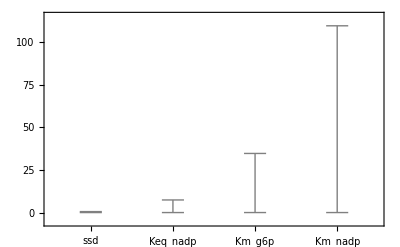

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```